# Least Squares/Data Fitting Homework (MTH 616)

1. Question:  Find the least squares solution to 
x1 + x2 = 4
2x1 + x2 = -2
x1 - x2 = 1.

```mathematica
(*Here are the matrices a, b*)
a = {{1,1},{2,1},{1,-1}};
b = {{4},{-2},{1}};
MatrixForm[a]
MatrixForm[b]
```

(1 | 1
2 | 1
1 | -1)

(4
-2
1)

```mathematica
(*Solution is given by*)
(soln = Inverse[Transpose[a].a].Transpose[a].b ) // MatrixForm
```

(1/14
2/7)

The least squares solution is x1 = 1/14, x2 = 2/7.

1b. Find the point on the plane spanned by (1,2,1) and (1,1,-1) that is closest to (4,-2,1).

```mathematica
N[a.soln]
```

{{0.357143},{0.428571},{-0.214286}}

2. Question: Find the best parabola y=ax^2 + bx +c that best fits the data (-1,0), (0,1), (1,3), (2,5).

```mathematica
a = {{1, -1, 1},{0,0,1},{1,1,1},{4,2,1}};
b = {0,1,3,5};
MatrixForm[a]
MatrixForm[b]
(soln = Inverse[Transpose[a].a].Transpose[a].b ) // MatrixForm
N[soln]
```

(1 | -1 | 1
0 | 0 | 1
1 | 1 | 1
4 | 2 | 1)

(0
1
3
5)

(1/4
29/20
23/20)

{0.25,1.45,1.15}

Best fit parabola is (1/4)x^2 + (29/20)x + 23/20.

```mathematica
(*Alternate Method*)
data1 = {{-1,0},{0,1},{1,3},{2,5}};
quad =Fit[data1, {1, x, x^2}, x]
```

1.15+1.45 x+0.25 x^2

Note: Here is a graph of the data points and the best fit parabola.

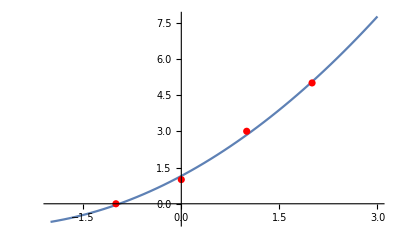

```mathematica
Show[Plot[quad, {x, -2, 3}], ListPlot[data1, PlotStyle -> Red]]
```

3.

3.04649-0.0253934 x

4.675-0.0608333 x

2.2593

2.78917

{{x→-37.5493}}

{{x→11.0959}}

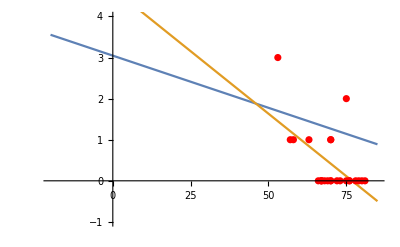

```mathematica
data1 = {{53, 3},{75,2},{57,1},{58,1},{63,1},{70,1},{70,1}};
data2 = {{53, 3},{75,2},{57,1},{58,1},{63,1},{70,1},{70,1}, {66,0},{67,0},{67,0},{67,0},{68,0},{69,0},{70,0},{70,0},{72,0},{73,0},{75,0},{76,0},{76,0},{78,0},{79,0},{80,0},{81,0}};

lin1 = Fit[data1,{1,x},x]
lin2 = Fit[data2,{1,x},x]

lin1 /. (x->31)  (*Plug x=31 into lin1*)
lin2 /. (x->31)  (*Plug x=31 into lin2*)

Solve[lin1 == 4, x] (*Solve for when average number of failures is 4*)
Solve[lin2 == 4, x]

Show[Plot[{lin1, lin2}, {x,-20, 85}], ListPlot[data2, PlotStyle -> Red], PlotRange -> {-1,4}]
```

For part (a), the linear regression using only the data points where a failure occurs gives y = 3.04 - .025x, which predicts an average of 2.26 failures at x=31 degrees.  When x = -37 degrees F, the average number of failures is 4.  

For part (b), the linear regression using all the data points gives an average failure of y=4.675 - .06x, predicting an average of 2.78 failures when x=31 degrees.  When x=11 degrees F, there will be an average of 4 failures.

4. Question: Find the values a0, a1, b1 for which a0 + a1 cos(x) + b1 sin(x) best fits the given data points (see data below)

```mathematica
(* One Method *)
data2 = {{-3,-1.5},{-2,-1},{-1,-.5},{0,0},{1,.5},{2,1},{3,1.5}};
MatrixForm[data2]
```

(-3 | -1.5
-2 | -1
-1 | -0.5
0 | 0
1 | 0.5
2 | 1
3 | 1.5)

-1.58494×10^-16+1.75954×10^-18 Cos[x]+0.991576 Sin[x]

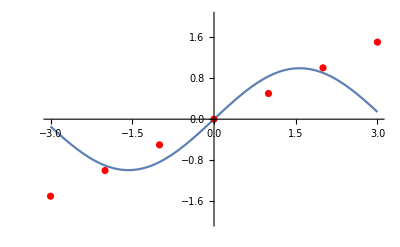

```mathematica
trig = Fit[data2, {1, Cos[x], Sin[x]}, x]
Show[Plot[trig, {x, -3, 3}], ListPlot[data2, PlotStyle -> Red], PlotRange -> {-2,2}]
```

```mathematica
(* Direct Method *)
a = {{1, Cos[-3],Sin[-3]},{1, Cos[-2],Sin[-2]},{1, Cos[-1],Sin[-1]}, {1, Cos[0],Sin[0]},{1, Cos[1],Sin[1]},{1, Cos[2],Sin[2]},{1, Cos[3],Sin[3]}};
b = {-1.5, -1, -.5, 0, .5, 1, 1.5};
MatrixForm[a]
MatrixForm[b]
MatrixForm[Inverse[Transpose[a].a].Transpose[a].b]
```

(1 | Cos[3] | -Sin[3]
1 | Cos[2] | -Sin[2]
1 | Cos[1] | -Sin[1]
1 | 1 | 0
1 | Cos[1] | Sin[1]
1 | Cos[2] | Sin[2]
1 | Cos[3] | Sin[3])

(-1.5
-1
-0.5
0
0.5
1
1.5)

(0.
0.
0.991576)

The best fit trig function is, up to rounding of very small numbers, .99 sin(x).

5. (See sheet for problem)

```mathematica
a = Table[{1, Cos[x], Sin[x]}, {x, -3.1, 3.1,.1}];
b = Table[x/2, {x, -3.1,3.1,.1}];
MatrixForm[Inverse[Transpose[a].a].Transpose[a].b]
```

(1.07553×10^-16
-2.35922×10^-16
1.00039)

```mathematica
data = Table[{x, x/2}, {x, -3.1, 3.1, .1}];
Fit[data, {1, Cos[x],Sin[x]},x]
```

6.72756×10^-17-1.18468×10^-16 Cos[x]+1.00039 Sin[x]

5a,b.  Up to very small rounding, we get the function 1.00039 sin(x), which was very close to .991sin(x) from #4.  Note this is very close to the Fourier Coefficients a0 = 0, a1 = 0, b1 = 1 for f(x) = x/2.

(1.11022×10^-16
-1.31839×10^-16
1.00039
1.52656×10^-16
-0.500785)

6.57691×10^-17-2.58046×10^-16 Cos[x]-1.69136×10^-17 Cos[2 x]+1.00039 Sin[x]-0.500785 Sin[2 x]

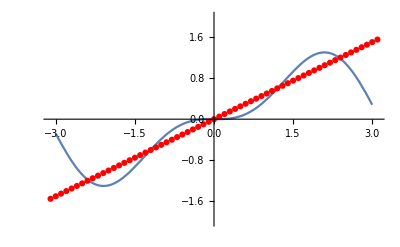

```mathematica
(*Part c, done two different ways *)
a = Table[{1, Cos[x], Sin[x], Cos[2x],Sin[2x]}, {x, -3.1, 3.1,.1}];
b = Table[x/2, {x, -3.1,3.1,.1}];
MatrixForm[Inverse[Transpose[a].a].Transpose[a].b]

data = Table[{x, x/2}, {x, -3.1, 3.1, .1}];
trig = Fit[data, {1, Cos[x],Sin[x], Cos[2x],Sin[2x]},x]

Show[Plot[trig, {x, -3, 3}], ListPlot[data, PlotStyle -> Red], PlotRange -> {-2,2}]
```

The resulting trigonometric polynomial is, up to a few decimal places, Sin(x) - .5 Sin(2x), which is the second-order Fourier approximation.